```mathematica
(*Results=Import["C:\\Users\\Owner\\Desktop\\PercolationThresholdForPyrochlore\\simulationThreshold.txt", "Table"]*)
```

```mathematica
Results2=0;
Results4=0;
Results6=0;
Results8=0;
Results10=0;
Results12=0;
Results14=0;
Results16=0;
```

```mathematica
(*Results2Im=Import["C:\\Users\\Owner\\Desktop\\Temp Percolation\\ThresholdTemp\\simulationThresholdSizes.txt", {"Data",Range[1,30],{5,7}}];
Results4Im=Import["C:\\Users\\Owner\\Desktop\\Temp Percolation\\ThresholdTemp\\simulationThresholdSizes.txt", {"Data",Range[31,60],{5,7}}];
Results6Im=Import["C:\\Users\\Owner\\Desktop\\Temp Percolation\\ThresholdTemp\\simulationThresholdSizes.txt", {"Data",Range[61,90],{5,7}}];
Results8Im=Import["C:\\Users\\Owner\\Desktop\\Temp Percolation\\ThresholdTemp\\simulationThresholdSizes.txt", {"Data",Range[91,120],{5,7}}];
Results10Im=Import["C:\\Users\\Owner\\Desktop\\Temp Percolation\\ThresholdTemp\\simulationThresholdSizes.txt", {"Data",Range[121,150],{5,7}}];*)
Results2Im=Import["/Users/haz4z/Desktop/Temp/simulationThresholdSizes1000TrialsFineScale.txt", {"Data",Range[1,21],{5,7}}];
Results4Im=Import["/Users/haz4z/Desktop/Temp/simulationThresholdSizes1000TrialsFineScale.txt", {"Data",Range[22,42],{5,7}}];
Results6Im=Import["/Users/haz4z/Desktop/Temp/simulationThresholdSizes1000TrialsFineScale.txt", {"Data",Range[43,63],{5,7}}];
Results8Im=Import["/Users/haz4z/Desktop/Temp/simulationThresholdSizes1000TrialsFineScale.txt", {"Data",Range[64,84],{5,7}}];
Results10Im=Import["/Users/haz4z/Desktop/Temp/simulationThresholdSizes1000TrialsFineScale.txt", {"Data",Range[85,105],{5,7}}];
Results12Im=Import["/Users/haz4z/Desktop/Temp/simulationThresholdSizes1000TrialsFineScale.txt", {"Data",Range[106,126],{5,7}}];
Results14Im=Import["/Users/haz4z/Desktop/Temp/simulationThresholdSizes1000TrialsFineScale.txt", {"Data",Range[127,147],{5,7}}];
Results16Im=Import["/Users/haz4z/Desktop/Temp/simulationThresholdSizes1000TrialsFineScale.txt", {"Data",Range[148,168],{5,7}}];
```

```mathematica
Results2Im[[All]]
```

{{0.6,11},{0.61,11},{0.62,5},{0.63,15},{0.64,21},{0.65,29},{0.66,40},{0.67,38},{0.68,53},{0.69,50},{0.7,60},{0.71,75},{0.72,99},{0.73,109},{0.74,117},{0.75,148},{0.76,154},{0.77,172},{0.78,176},{0.79,180},{0.8,192},{0.81,195},{0.82,196},{0.83,196},{0.84,199},{0.85,200},{0.86,200},{0.87,200},{0.88,200},{0.89,200}}

```mathematica
Results2=Results2Im;
Results4=Results4Im;
Results6=Results6Im;
Results8=Results8Im;
Results10=Results10Im;
Results12=Results12Im;
Results14=Results14Im;
Results16=Results16Im;
Results2[[All,2]]=Results2Im[[All,2]]/1000.0
Results4[[All,2]]=Results4Im[[All,2]]/1000.0
Results6[[All,2]]=Results6Im[[All,2]]/1000.0
Results8[[All,2]]=Results8Im[[All,2]]/1000.0
Results10[[All,2]]=Results10Im[[All,2]]/1000.0
Results12[[All,2]]=Results12Im[[All,2]]/1000.0
Results14[[All,2]]=Results14Im[[All,2]]/1000.0
Results16[[All,2]]=Results16Im[[All,2]]/1000.0
```

{0.291,0.302,0.294,0.309,0.314,0.334,0.33,0.357,0.369,0.358,0.347,0.396,0.376,0.379,0.419,0.408,0.391,0.427,0.39,0.412,0.411}

{0.282,0.308,0.29,0.344,0.362,0.354,0.362,0.387,0.381,0.405,0.421,0.45,0.441,0.466,0.488,0.489,0.494,0.542,0.541,0.515,0.573}

{0.27,0.303,0.32,0.308,0.36,0.357,0.384,0.417,0.412,0.435,0.479,0.489,0.515,0.516,0.543,0.563,0.594,0.627,0.636,0.661,0.698}

{0.255,0.272,0.306,0.331,0.367,0.367,0.399,0.425,0.448,0.456,0.511,0.547,0.561,0.572,0.615,0.659,0.696,0.739,0.748,0.78,0.772}

{0.181,0.25,0.285,0.296,0.336,0.385,0.366,0.475,0.459,0.488,0.563,0.581,0.616,0.647,0.684,0.731,0.767,0.805,0.826,0.861,0.853}

{0.169,0.214,0.265,0.292,0.325,0.372,0.379,0.473,0.483,0.538,0.579,0.625,0.681,0.709,0.773,0.783,0.846,0.863,0.892,0.906,0.937}

{0.17,0.187,0.245,0.267,0.286,0.324,0.366,0.461,0.505,0.548,0.621,0.698,0.721,0.75,0.822,0.861,0.883,0.914,0.929,0.953,0.968}

{0.13,0.179,0.183,0.246,0.298,0.322,0.404,0.45,0.517,0.588,0.671,0.709,0.768,0.817,0.862,0.894,0.927,0.942,0.971,0.981,0.983}

```mathematica
Results2
```

{{0.6,0.055},{0.61,0.055},{0.62,0.025},{0.63,0.075},{0.64,0.105},{0.65,0.145},{0.66,0.2},{0.67,0.19},{0.68,0.265},{0.69,0.25},{0.7,0.3},{0.71,0.375},{0.72,0.495},{0.73,0.545},{0.74,0.585},{0.75,0.74},{0.76,0.77},{0.77,0.86},{0.78,0.88},{0.79,0.9},{0.8,0.96},{0.81,0.975},{0.82,0.98},{0.83,0.98},{0.84,0.995},{0.85,1.},{0.86,1.},{0.87,1.},{0.88,1.},{0.89,1.}}

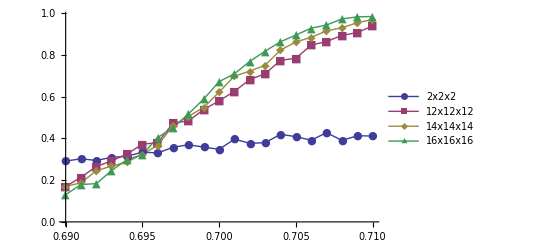

```mathematica
(*ListPlot[{Results2,Results4,Results6,Results8,Results10},Filling->Axis,PlotMarkers->{Automatic,Small},BaseStyle->{FontSize->16}]*)
ListLinePlot[{Results2,Results12,Results14,Results16},PlotMarkers->{Automatic,Small},BaseStyle->{FontSize->15},PlotLegends->Placed[{"2x2x2","12x12x12","14x14x14","16x16x16"},{.85,.5}]]
```